```mathematica
boatDens = 1.225*(1.875/2)+710*(.125/2) ;(*Boat density (kg/m^3)*)
deckDens = 710* 0.003175 ;(*Deck area density (kg/m^2*)
mCargo = .8; (*Cargo mass (kg)*)
mMast = (π*(3/8*1/2)^2*19.685*(2.7/0.0610237))/1000; (*Mass of mast (kg)*)
comMast = {0,0,.3}; (*COM of mast (m)*)
comCargo = {0,0,.027}; (*COM of cargo (m)*)
```

```mathematica
.2*.5*710*.003
```

0.213

```mathematica
Clear[boat,mass,com,submerged,submass,water,cob,arm]
boatFunc[n_?NumberQ,d_?NumberQ,xLen_?NumberQ,xVal_,zVal_]:=2*Abs[y/n]^1.5+d*(xVal^2/xLen^2)≤zVal≤d
boat= ImplicitRegion[boatFunc[.75,.1,.25,x,z] ,{x,y,z}];
mass :=mass= boatDens*RegionMeasure[boat]
massTot:=mass+mCargo+mMast+deckDens*RegionMeasure[ImplicitRegion[boatFunc[.75,.1,.25,x,.1],{x,y}]]
com:=com=(N[RegionCentroid[boat]]*mass+mCargo*comCargo+mMast*comMast)/massTot
submerged[d_,t_]:=ImplicitRegion[2*(Abs[y/2]^2+Abs[x/5]^4)<z<2&&If[t<90,z<N[Tan[t Degree]]*y+d,z>N[Tan[t Degree]]*y+d],{{x,-5,5},{y,-2,2},{z,0,2}}]
submass[d_,t_]:=1000*N[RegionMeasure[submerged[d,t]]]
water[t_]:=water[t]=FindRoot[submass[d,t]==mass,{d,-20,20}]
cob[t_]:=cob[t]=N[RegionCentroid[submerged[d,t]/.water[t]]]
arm[t_?NumberQ]:=Cross[cob[t]-com,{0,-Sin[t Degree],Cos[t Degree]}][[1]]
```

```mathematica
arm[120]
```

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[2 (1/625 Abs[«1»]^4+1/4 Abs[«1»]^2)<z<2&&z>d-1.73205 y&&-5≤x≤5&&-2≤y≤2&&0≤z≤2,{x,y,z}].

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[2. (0.0016 Abs[«1»]^4+0.25 Abs[«1»]^2)<z<2.&&z>d-1.73205 y&&-5.≤x≤5.&&-2.≤y≤2.&&0.≤z≤2.,{x,y,z}].

0.694896

```mathematica
Manipulate[RegionPlot3D[boatFunc[.75,d,.25,x,z],{x,-.249,.249},{y,-.1,.1},{z,0,.15},AxesLabel->Automatic,BoxRatios->Automatic],{d,.1,.15}]
```

```mathematica
points = Map[arm,Range[0,180,20]]
```

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[2 (1/625 Abs[«1»]^4+1/4 Abs[«1»]^2)<z<2&&z<0.+d&&-5≤x≤5&&-2≤y≤2&&0≤z≤2,{x,y,z}].

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[2. (0.0016 Abs[«1»]^4+0.25 Abs[«1»]^2)<z<2.&&z<0.+d&&-5.≤x≤5.&&-2.≤y≤2.&&0.≤z≤2.,{x,y,z}].

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[2 (1/625 Abs[«1»]^4+1/4 Abs[«1»]^2)<z<2&&z<d+0.36397 y&&-5≤x≤5&&-2≤y≤2&&0≤z≤2,{x,y,z}].

General::stop: Further output of RegionMeasure::nmet will be suppressed during this calculation.

{0.,0.343572,0.829417,2.11163,2.24749,1.55719,0.677914,-0.283205,-1.20947,1.12631×10^-18}

```mathematica
angles = Range[0,180,20]
newPoints = Transpose[{angles,points}]
```

{0,20,40,60,80,100,120,140,160,180}

{{0,0.},{20,0.343572},{40,0.829417},{60,2.11163},{80,2.24749},{100,1.55719},{120,0.677914},{140,-0.283205},{160,-1.20947},{180,1.12631×10^-18}}

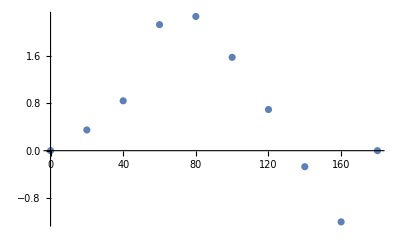

```mathematica
ListPlot[newPoints]
```

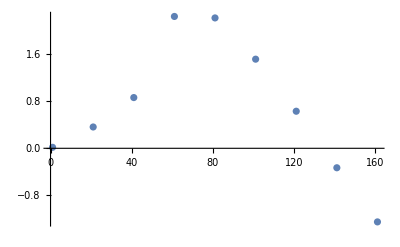

```mathematica
ListPlot[newPoints]
```

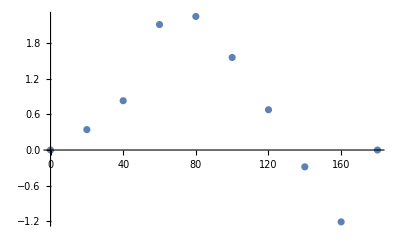

```mathematica
ListPlot[newPoints]
```

```mathematica
boatFunc[n_,d_,xVal_]:=Exp[Abs[y/(n*(xVal^2-4))]]+(xVal^2-4)/6≤z≤d
RegionMeasure[ImplicitRegion[boatFunc[.4,1,x],{x,y,z}]]
```

7.99093